# IGraph/M

## use igraph from Mathematica

This notebook can (and should) be opened using the command IGDocumentation[]. When opened like this, it cannot be saved, so feel free to re-evaluate cells and experiment.

The documentation is currently incomplete. Contributions are welcome!

## Basic usage

The package can be loaded using

```mathematica
<<IGraphM`
```

Evaluate IGDocumentation[] to get started.

The list of included functions is below. Notice that their names always have the IG prefix. Click on the name of a function to see its usage message.

```mathematica
?IGraphM`*
```

Or just type a question mark followed by the symbol’s name:

```mathematica
?IGVersion
```

IGVersion[] returns the IGraph/M version along with the version of the igraph library in use.

```mathematica
IGVersion[]
```

IGraph/M 0.1.3dev
igraph 0.8.0-pre+2e63cab (Sep 24 2015)
Mac OS X x86 (64-bit)

IGraph/M functions work directly with Mathematica’s built-in Graph datatype. No new special graph datatype is introduced.

Let’s take a look at a few examples. Let us first generate a graph using the built-in functions of Mathematica.

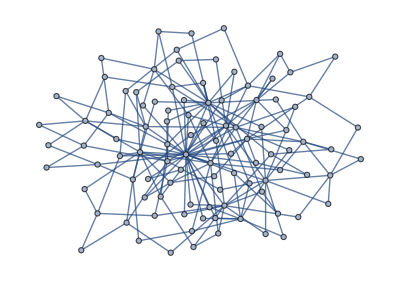

```mathematica
g=RandomGraph[BarabasiAlbertGraphDistribution[100,2]]
```

We can compute the betweenness centrality of each vertex using IGraph/M ...

```mathematica
IGBetweenness[g]
```

{319.918,40.9935,2082.21,401.721,399.938,893.634,101.102,551.497,459.737,86.0977,6.85269,513.,10.1343,209.478,339.164,400.914,208.847,185.081,48.9147,18.9692,158.822,107.222,0.,52.2804,62.3343,6.85269,115.843,0.,118.61,26.7484,166.194,48.8268,112.282,82.3053,13.8194,28.0069,0.,59.3196,181.336,17.1116,87.6861,11.1325,25.001,50.5918,9.22623,141.187,66.8427,6.76111,6.04915,33.8707,2.31667,11.1878,15.4,168.991,3.83333,13.8759,0.,3.36667,10.9237,10.8467,18.839,10.9259,0.,17.3634,20.7156,57.8421,54.6128,10.3748,5.38939,37.2966,20.939,24.9818,15.8576,3.92424,8.61515,2.20536,18.3984,6.52778,0.,2.86667,6.85269,6.34746,20.3465,16.3437,20.5251,8.35794,1.7,17.3634,9.0873,20.0812,48.7712,5.80119,12.3539,0.,3.68611,5.5623,10.1734,0.,3.33333,19.4284}

... or using Mathematica, and obtain the same result.

```mathematica
BetweennessCentrality[g]
```

{319.918,40.9935,2082.21,401.721,399.938,893.634,101.102,551.497,459.737,86.0977,6.85269,513.,10.1343,209.478,339.164,400.914,208.847,185.081,48.9147,18.9692,158.822,107.222,0.,52.2804,62.3343,6.85269,115.843,0.,118.61,26.7484,166.194,48.8268,112.282,82.3053,13.8194,28.0069,0.,59.3196,181.336,17.1116,87.6861,11.1325,25.001,50.5918,9.22623,141.187,66.8427,6.76111,6.04915,33.8707,2.31667,11.1878,15.4,168.991,3.83333,13.8759,0.,3.36667,10.9237,10.8467,18.839,10.9259,0.,17.3634,20.7156,57.8421,54.6128,10.3748,5.38939,37.2966,20.939,24.9818,15.8576,3.92424,8.61515,2.20536,18.3984,6.52778,0.,2.86667,6.85269,6.34746,20.3465,16.3437,20.5251,8.35794,1.7,17.3634,9.0873,20.0812,48.7712,5.80119,12.3539,0.,3.68611,5.5623,10.1734,0.,3.33333,19.4284}

Let us now assign weights to the edges. Many IGraph/M functions, including IGBetweenness, support edge weights.

```mathematica
wg=SetProperty[g,EdgeWeight->RandomReal[1,EdgeCount[g]]];
```

```mathematica
IGBetweenness[wg]
```

{258.,25.,1877.,201.,329.,1213.,145.,528.,743.,489.,0.,1108.,9.,509.,435.,112.,73.,21.,204.,27.,404.,700.,0.,127.,38.,459.,114.,0.,183.,126.,206.,24.,174.,114.,28.,6.,478.,3.,127.,116.,120.,236.,115.,0.,0.,579.,94.,0.,4.,53.,35.,30.,57.,34.,0.,0.,0.,0.,57.,0.,547.,0.,0.,0.,35.,19.,51.,0.,0.,31.,22.,0.,0.,10.,4.,24.,160.,22.,0.,13.,0.,19.,0.,35.,93.,4.,0.,0.,0.,0.,19.,0.,22.,68.,15.,0.,0.,0.,79.,182.}

Notice that Mathematica 10.2 does not include functionality to compute weighted betweenness. BetweennessCentrality[] ignores the weights.

```mathematica
BetweennessCentrality[wg]
```

{319.918,40.9935,2082.21,401.721,399.938,893.634,101.102,551.497,459.737,86.0977,6.85269,513.,10.1343,209.478,339.164,400.914,208.847,185.081,48.9147,18.9692,158.822,107.222,0.,52.2804,62.3343,6.85269,115.843,0.,118.61,26.7484,166.194,48.8268,112.282,82.3053,13.8194,28.0069,0.,59.3196,181.336,17.1116,87.6861,11.1325,25.001,50.5918,9.22623,141.187,66.8427,6.76111,6.04915,33.8707,2.31667,11.1878,15.4,168.991,3.83333,13.8759,0.,3.36667,10.9237,10.8467,18.839,10.9259,0.,17.3634,20.7156,57.8421,54.6128,10.3748,5.38939,37.2966,20.939,24.9818,15.8576,3.92424,8.61515,2.20536,18.3984,6.52778,0.,2.86667,6.85269,6.34746,20.3465,16.3437,20.5251,8.35794,1.7,17.3634,9.0873,20.0812,48.7712,5.80119,12.3539,0.,3.68611,5.5623,10.1734,0.,3.33333,19.4284}

Let us delete the minimum feedback edge set to obtain an acyclic graph:

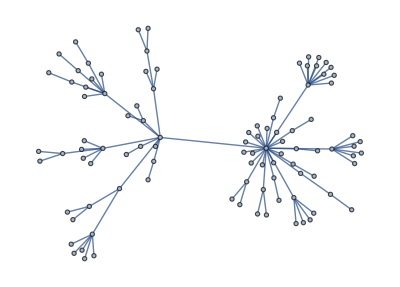

```mathematica
acg=EdgeDelete[g,IGFeedbackArcSet[g]]
```

And try out a few of igraph’s layout algorithms.

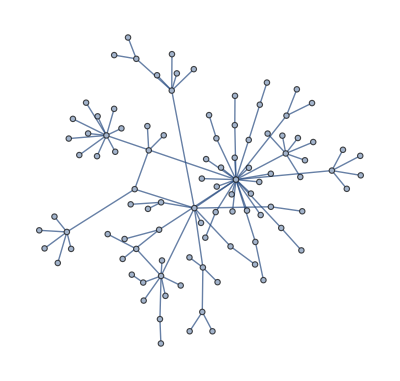
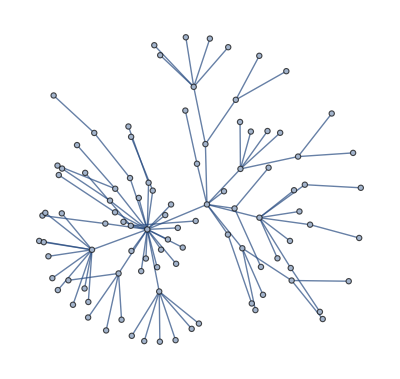
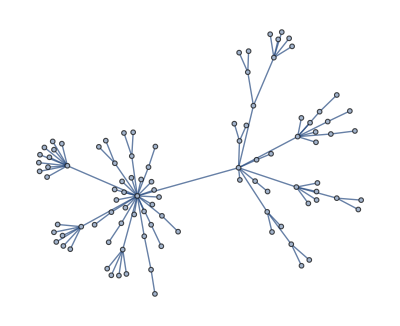

```mathematica
{IGLayoutGraphOpt[acg],IGLayoutKamadaKawai[acg],IGLayoutFruchtermanReingold[acg]}
```

Layout functions typically have many options to tune:

```mathematica
Options[IGLayoutGraphOpt]
```

{MaxIterations→500,NodeCharge→0.001,NodeMass→30,SpringLength→0,SpringConstant→1,MaxStepMovement→5,Continue→False}

Increasing the number of iterations will usually improve the result.

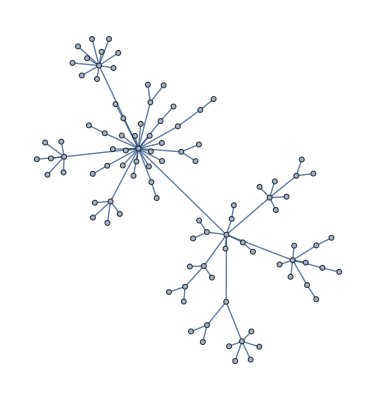

```mathematica
IGLayoutGraphOpt[acg,"MaxIterations"->5000]
```

A final note

Please refer to the usage messages for information on how to use each function. For more information on the meaning of various function options, the algorithms used by the functions, references, etc. please refer to the C/igraph documentation. The igraph documentation provides article references for most nontrivial algorithms. Note that IGraph/M is currently built using the development version of igraph (0.8.0-pre) while the online igraph documentation is for the last released version (0.7.1). Some new functionality may not yet be described in the online documentation.

The following sections provide general information on each functionality area, and show common usage patterns.

## Graph creation

All the graph creation functions in IGraph/M take any standard Mathematica Graph option such as VertexLabels, GraphStyle, VertexStyle, etc.

```mathematica
IGLCF[{5,-5},7,GraphStyle->"SmallNetwork"]
```

-Graphics-

Many included graph creation functions implement random graph models. These use igraph’s (not Mathematica’s) random number generator, which can be re-seeded using IGSeedRandom[].

#### IGMakeLattice

IGMakeLattice[{d_1,d_2,…}] creates a lattice graph of the given dimensions. The available options are:

"Radius" controls the size of the neighbourhood within which vertices will be connected.

"Periodic"→True to creates a periodic lattice.

"Mutual"→True inserts directed edges in both directions when DirectedEdges→True is used.

#### IGDegreeSequenceGame

IGDegreeSequenceGame takes the following values for its Method option:

"Simple" may generate both self-loops and multiple edges.

"SimpleNoMultiple" avoids self-loops and multiple edges, but it does not guarantee uniform sampling from the space of all graphs with the given degree sequence.

"VigerLatapy" can sample undirected, connected simple graphs uniformly and uses Monte-Carlo methods to randomize the graphs. This generator should be favoured if undirected and connected graphs are to be generated and execution time is not a concern. igraph uses the original implementation of Fabien Viger; see http://www-rp.lip6.fr/~latapy/FV/generation.html and the paper cited on it for the details of the algorithm.

## Structural properties

### Betweenness centrality

IGBetwenness[] and IGBetwennessEstimate[] have a "UseBigInt" option, set to True by default.

```mathematica
Options[IGBetweenness]
```

{UseBigInt→True}

Setting this to False will speed up betweenness calculation significantly but it may give incorrect results for large graphs with lots of symmetries such as GridGraph[{40,40}], due to integer overflow.

### Topological sorting and acyclic graphs

IGFeedbackArcSet[] returns a set of edges the removal of which makes the graph acyclic. With "Exact"→True it finds a minimal feedback arc set. With "Exact"→False it finds a feedback arc set (not necessarily minimal) using the heuristic of Eades, Lin and Smyth (1993).

### Chordal graphs

The maximum cardinality search algorithm visits the vertices of the graph in such an order so that every time the vertex with the most already visited neighbors is visited next. The visiting order is animated below:

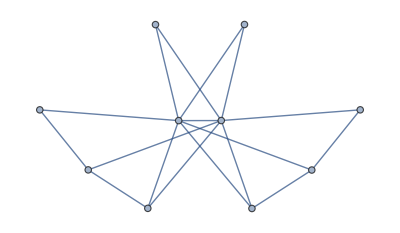
```mathematica
g=-Graphics-;
```

```mathematica
seq=InversePermutation@IGMaximumCardinalitySearch[g]
```

{7,6,2,9,8,4,5,3,10,1}

```mathematica
Table[
HighlightGraph[
Graph[g,VertexLabels->"Name"],
Take[seq,-i]
],
{i,1,10}
]//ListAnimate
```

## Isomorphism

igraph implements three isomorphism testing algorithms: BLISS, VF2 and LAD. These support slightly different functionality. Most of IGraph/M’s isomorphism related functions include the name of the algorithm as a prefix, e.g. IGBlissIsomorphicQ. The exceptions are IGIsomorphicQ[] and IGSubisomorphicQ[], which use igraph’s default method for selecting the best option for the current type of graph.

Functions named as …GetIsomorphism will find a single isomorphism. Functions names as …FindIsomorphisms can find multiple isomorphisms. Both return a result in a format compatible with the built-in FindGraphIsomorphism.

### BLISS

See http://www.tcs.hut.fi/Software/bliss/ and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470920858320

The current implementation only supports undirected graphs.

```mathematica
?IGBliss*
```

Bliss functions take a "SplittingHeuristics" option, which can influence the performance of the method. Possible values are:

"First" – First non-unit cell. Very fast but may result in large search spaces on difficult graphs. Use for large but easy graphs.

"FirstSmallest" – First smallest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstLargest" – First largest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstMaximallyConnected" – First maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstSmallestMaximallyConnected" – First smallest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstLargestMaximallyConnected" – First largest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

Note: The result of the IGBlissCanonicalLabeling, IGBlissCanonicalPermutation and IGBlissanonicalGraph functions depend on the choice of "SplittingHeuristics". See the Bliss documentation for more information.

### VF2

```mathematica
?IGVF2*
```

VF2 supports vertex coloured and edge coloured graphs. Colours can be provided as a pair of integer lists using the "VertexColors" or "EdgeColors" options.

### LAD

See http://liris.cnrs.fr/csolnon/LAD.html and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470934622128

```mathematica
?IGLAD*
```

With the "Induced"→True option LAD will search for induced subgraphs.



```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-]
```

True

```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

False

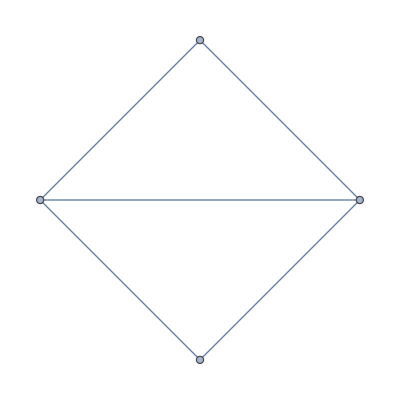
```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

True

## Maximum flow and connectivity

### Cohesive blocks

The following examples are based on the ones in the R/igraph documentation.

This is the network from the Moody-White paper:

J. Moody and D. R. White. Structural cohesion and embeddedness: A hierarchical concept of social groups. American Sociological Review, 68(1):103–127, Feb 2003.

```mathematica
mw=Graph[{"1"<->"2","1"<->"3","1"<->"4","1"<->"5","1"<->"6","2"<->"3","2"<->"4","2"<->"5","2"<->"7","3"<->"4","3"<->"6","3"<->"7","4"<->"5","4"<->"6","4"<->"7","5"<->"6","5"<->"7","5"<->"21","6"<->"7","7"<->"8","7"<->"11","7"<->"14","7"<->"19","8"<->"9","8"<->"11","8"<->"14","9"<->"10","10"<->"12","10"<->"13","11"<->"12","11"<->"14","12"<->"16","13"<->"16","14"<->"15","15"<->"16","17"<->"18","17"<->"19","17"<->"20","18"<->"20","18"<->"21","19"<->"20","19"<->"22","19"<->"23","20"<->"21","21"<->"22","21"<->"23","22"<->"23"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[mw]
```

{{{1,2,3,4,5,6,7,21,8,11,14,19,9,10,12,13,16,15,17,18,20,22,23},{1,2,3,4,5,6,7,21,19,17,18,20,22,23},{7,8,11,14,9,10,12,13,16,15},{1,2,3,4,5,6,7},{7,8,11,14}},{1,2,2,5,3}}

```mathematica
CommunityGraphPlot[mw,Rest@blocks,CommunityRegionStyle->Table[Directive[Opacity[0.5],ColorData[96][i]],{i,Length[blocks]-1}]]
```

-Graphics-

```mathematica
cohesion
```

{1,2,2,5,3}

Science camp network

```mathematica
sc=Graph[{"Pauline"<->"Jennie","Pauline"<->"Ann","Jennie"<->"Ann","Jennie"<->"Michael","Michael"<->"Ann","Holly"<->"Jennie","Jennie"<->"Lee","Michael"<->"Lee","Harry"<->"Bert","Harry"<->"Don","Don"<->"Bert","Gery"<->"Russ","Russ"<->"Bert","Michael"<->"John","Gery"<->"John","Russ"<->"John","Holly"<->"Pam","Pam"<->"Carol","Holly"<->"Carol","Holly"<->"Bill","Bill"<->"Pauline","Bill"<->"Michael","Bill"<->"Lee","Harry"<->"Steve","Steve"<->"Don","Steve"<->"Bert","Gery"<->"Steve","Russ"<->"Steve","Pam"<->"Brazey","Brazey"<->"Carol","Pam"<->"Pat","Brazey"<->"Pat","Carol"<->"Pat","Holly"<->"Pat","Gery"<->"Pat"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[sc]
```

{{{Pauline,Jennie,Ann,Michael,Holly,Lee,Harry,Bert,Don,Gery,Russ,John,Pam,Carol,Bill,Steve,Brazey,Pat},{Harry,Bert,Don,Steve},{Holly,Pam,Carol,Brazey,Pat},{Pauline,Jennie,Ann,Michael,Lee,Bill}},{2,3,3,3}}

```mathematica
CommunityGraphPlot[sc,Rest@blocks,CommunityRegionStyle->ColorData[96],ImageSize->Large]
```

-Graphics-

## Layout algorithms

```mathematica
?IGLayout*
```

Most layout algorithms take a "MaxIterations" option. This controls either the maximum number of iterations performed by the algorithm or the exact number of iterations, depending on the specific algorithm and settings. The option name is the same for all functions to make it easier to interchange them when visualizing dynamic graphs.

Many layout algorithms can take the existing vertex coordinates as starting points. This is controlled by the "Continue" option. We can use this to visualize how the layout algorithms work …

```mathematica
g=IGLayoutRandom@RandomGraph[BarabasiAlbertGraphDistribution[100,1]];
ListAnimate@NestList[IGLayoutGraphOpt[#,"Continue"->True,"MaxIterations"->80]&,g,40]
```

… or to visualize dynamic graph processes such as adding edges to the graph one by one:

```mathematica
g=IGLayoutKamadaKawai@Graph[Range[25],{1<->25},VertexLabels->"Name"];
ListAnimate@NestList[
IGLayoutKamadaKawai[EdgeAdd[#,UndirectedEdge@@RandomSample[VertexList[#],2]],"MaxIterations"->15,"Continue"->True]&,
g,
30
]
```

### Drawing trees

IGLayoutRengoldTilford[] and IGLayoutRengoldTilfordCircular[] are designed for laying out trees. The following options are available:

"Roots" allows specifying one (for a tree) or more (for a forest) nodes to be used as the root node in the layout.

DirectedEdges → True lays out the graph so that directed edges are pointing form lower levels (near the root) towards higher ones (away from the root).

### Gallery

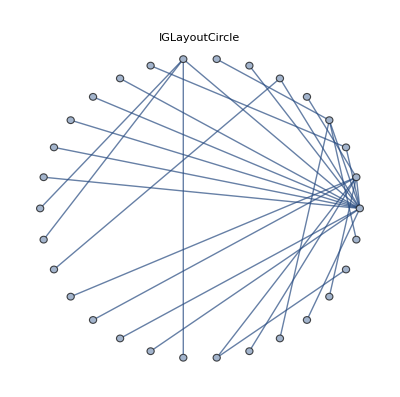
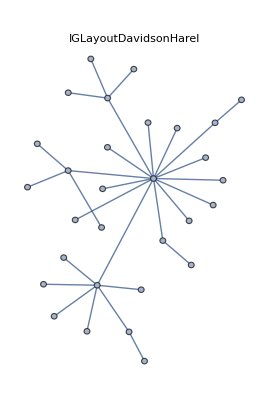
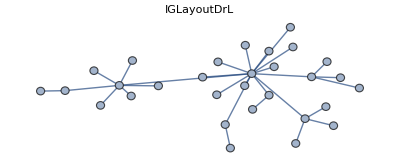
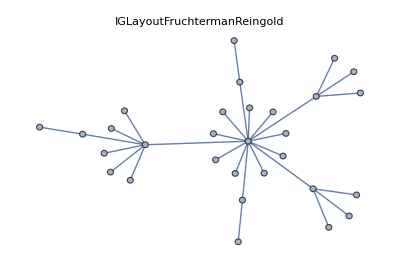
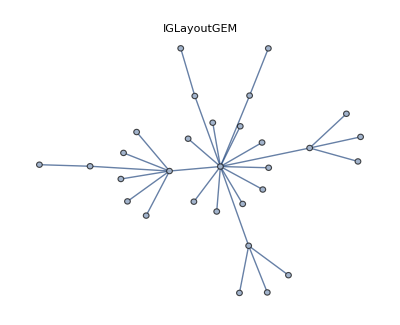
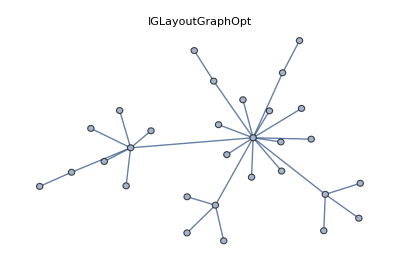
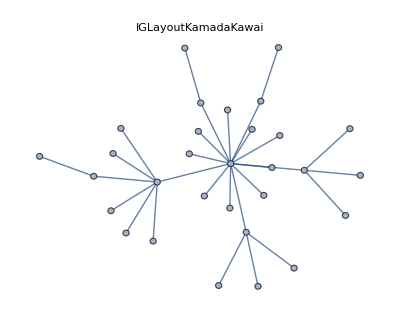
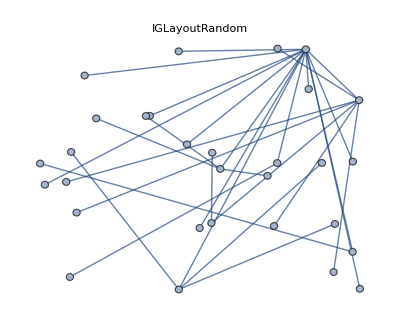
-Graphics- | -Graphics- | -Graphics- | -Graphics3D-
-Graphics- | -Graphics3D- | -Graphics- | -Graphics-
-Graphics- | -Graphics3D- | -Graphics- | -Graphics-
-Graphics- | -Graphics3D- |  |

```mathematica
g=RandomGraph[BarabasiAlbertGraphDistribution[30,1]];
layouts=Graph[#[g],PlotLabel->#]&/@{IGLayoutCircle,IGLayoutDavidsonHarel,IGLayoutDrL,IGLayoutDrL3D,IGLayoutFruchtermanReingold,IGLayoutFruchtermanReingold3D,IGLayoutGEM,IGLayoutGraphOpt,IGLayoutKamadaKawai,IGLayoutKamadaKawai3D,IGLayoutRandom,IGLayoutReingoldTilford,IGLayoutReingoldTilfordCircular,IGLayoutSphere};
Grid@Partition[layouts,4,4,{1,1},""]
```

## Notes on other functions

### Random number generator

igraph’s random number generator can be seeded using

```mathematica
IGSeedRandom[123]
```

### IGData[]

The IGData[] function provides access to various useful datasets. In particular, it can list small directed graphs ordered based on their IGIsoclass[], i.e. the same order motif counting functions use.

```mathematica
IGData[]
```

{{AllDirectedGraphs,3},{AllDirectedGraphs,4},MANTriadLabels}

Here’s all size 3 directed graphs.

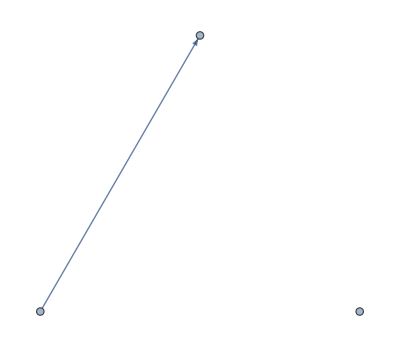
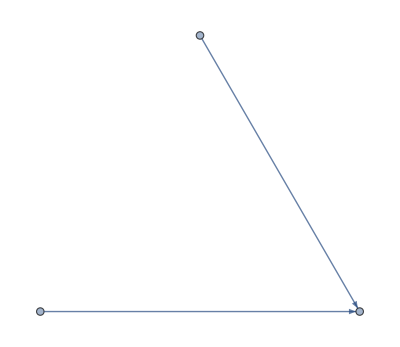
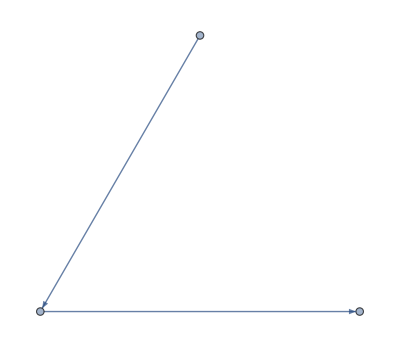
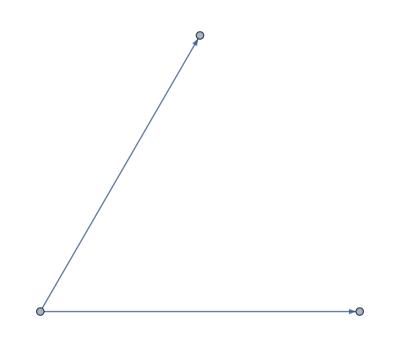
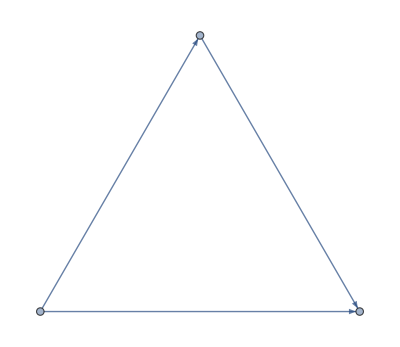
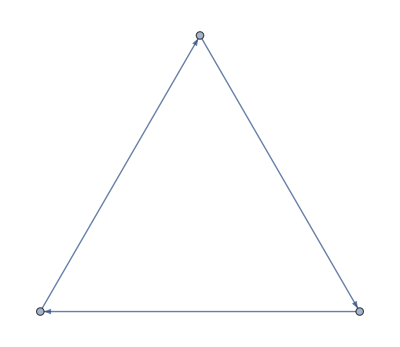
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row@IGData[{"AllDirectedGraphs",3}]
```

"MANTriadLabels" refers to the mutual, asymmetric, null labelling of triads used by IGTriadCensus[]. Each label is mapped to the corresponding graph, ordered based on their IGIsoclass. This is useful for converting the output of IGTriadCensus[] to a format compatible with IGMotifs[].